Articles for comparison:
R&I: https://arxiv.org/pdf/1202.2841.pdf
Dolgov et. al: https://arxiv.org/pdf/hep-ph/9703315.pdf
Mangano et. al: https://arxiv.org/pdf/hep-ph/0506164.pdf
Hannestad&Madsen: https://arxiv.org/pdf/astro-ph/9506015.pdf

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/stasya/prj/pyBBN/tests/standard_model_bbn

```mathematica
FileToNumLevel2[lines_]:=Module[{func, var, buf},
func = Function[x, var=StringToStream@x;buf=Read[var,Number];Close@var;buf];
Map[func, lines, {2}]
];
```

```mathematica
FileToNumLevel1[lines_]:=Module[{func, var, buf},
func = Function[x, var=StringToStream@x;buf=Read[var,Number];Close@var;buf];
Map[func, lines, {1}]
];
```

#### Elecrton neutrinos

```mathematica
rawlinesEl = Import["./output0015625/Electron_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesEl = StringSplit/@rawlinesEl[[2;;]];
linesEl = FileToNumLevel2[linesEl];
```

```mathematica
T= Last[linesEl][[2]];
distEl1=Last[linesEl][[3;;]];
yEl=FileToNumLevel1[StringSplit[rawlinesEl[[1]]][[4;;]]];
plotDataEl=Transpose[{yEl, distEl1}];
```

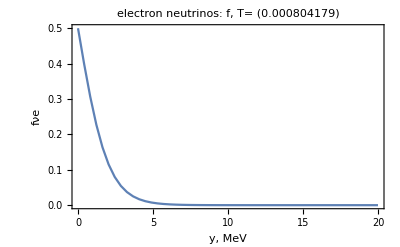

```mathematica
ListLinePlot[plotDataEl,PlotLabel->Style[#,Bold,15]&/@{"electron neutrinos: f, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fνe"},PlotRange->All]
```

#### Muon neutrinos

```mathematica
rawlinesμ = Import["./output0015625/Muon_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesμ = StringSplit/@rawlinesμ[[2;;]];
linesμ=FileToNumLevel2[linesμ];
```

```mathematica
Tμ= Last[linesμ][[2]];
distμ=Last[linesμ][[3;;]];
yμ=FileToNumLevel1[StringSplit[rawlinesμ[[1]]][[4;;]]];
plotDataμ=Transpose[{yμ, distμ}];
```

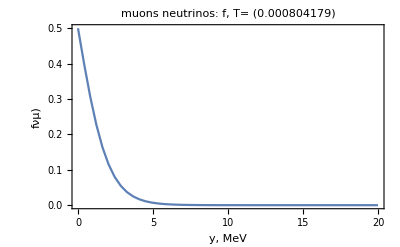

```mathematica
ListLinePlot[plotDataμ,PlotLabel->Style[#,Bold,15]&/@{"muons neutrinos: f, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fνμ)"},PlotRange->All]
```

## Final spectrum. Comparison with previous results (Fig. 10)

```mathematica
(*final-spectra-SM.eps*)
multiplier={#⟦1⟧,#⟦2⟧*(Exp[#⟦1⟧]+1)}&;
(*finalspectraSMTest2015Electron =multiplier/@Import["../tests/standard_model_bbn/spectrum_Electron neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015ElectronFunc = Interpolation[finalspectraSMTest2015Electron];
finalspectraSMTest2015Muon = multiplier/@Import["../tests/standard_model_bbn/spectrum_Muon neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015MuonFunc = Interpolation[finalspectraSMTest2015Muon];*)
```

```mathematica
plotfEl=Interpolation[multiplier/@plotDataEl];
plotfμ=Interpolation[multiplier/@plotDataμ];
```

```mathematica
finalspectraSMTest=Import["../../figures/Figures-sources/Final-spectra-SM/spectra-test-SM.dat","HeaderLines"->3];
```

```mathematica
finalspectranueSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-nue-noosc.tsv"];
finalspectranumuSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-numu-noosc.tsv"];
```

```mathematica
finalnueSMTestFunc=Interpolation[multiplier/@finalspectraSMTest[[All,{1,4}]]];
finalnumuSMTestFunc=Interpolation[multiplier/@finalspectraSMTest[[All,{1,8}]]];
```

```mathematica
finalspectranueSMDigitFunc=Interpolation[finalspectranueSMDigit[[All,{1,2}]]];
finalspectranumuSMDigitFunc=Interpolation[finalspectranumuSMDigit[[All,{1,2}]]];
```

InterpolatingFunction::dmval: Input value {0.000245143} lies outside the range of data in the interpolating function. Extrapolation will be used.

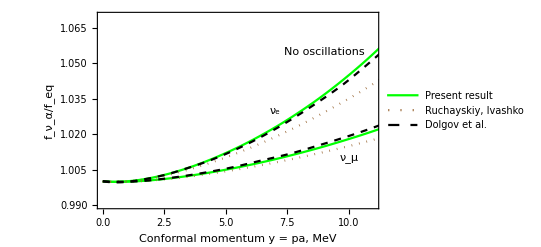

```mathematica
plt=Show[Plot[{
plotfEl[y],
plotfμ[y],
finalnueSMTestFunc[y],
finalnumuSMTestFunc[y],
finalspectranueSMDigitFunc[y],
finalspectranumuSMDigitFunc[y]
},{y,0,12},PlotRange->{{0,11},{0.99,1.07}},Frame->True,FrameLabel->{"Conformal momentum y = pa, MeV","f_ν_α/f_eq"},PlotStyle->{{Green},{Green},{Brown,Dotted},{Brown,Dotted},{Black,Dashed},{Black,Dashed}},Epilog->{Text["ν_e",{7,1.03}],Text["ν_μ",{10,1.01}],Text["No oscillations",{9,1.055}]},
PlotLegends->{"Present result",None,"Ruchayskiy, Ivashko",None,"Dolgov et al.",None}]]
Export["final-spectra-SM.eps",%];
```

### Mangano, Dolgov, Ruchaiskyi

```mathematica
ManganoNuEl=finalspectranueSMDigitFunc;
```

```mathematica
DolgovNuElBoltzmann=Import["../../figures/Figures-sources/Final-spectra-SM/DolgovVSMangano/DolgovBoltzmann.csv"];
```

```mathematica
DolgovNuElFermi=Import["../../figures/Figures-sources/Final-spectra-SM/DolgovVSMangano/DolgovFermi-Dirac.csv"];
```

```mathematica
DolgovNuElBoltzmannFunc=Interpolation[DolgovNuElBoltzmann];
DolgovNuElFermiFunc=Interpolation[DolgovNuElFermi];
```

InterpolatingFunction::dmval: Input value {0.000245143} lies outside the range of data in the interpolating function. Extrapolation will be used.

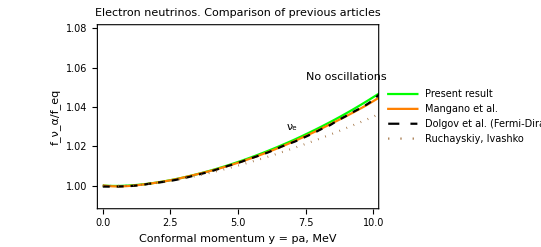

```mathematica
Show[Plot[{plotfEl[y],
ManganoNuEl[y], DolgovNuElFermiFunc[y]+1, finalnueSMTestFunc[y]
},{y,0,12},PlotRange->{{0,10},{0.99,1.08}},Frame->True,PlotLabel-> "Electron neutrinos. Comparison of previous articles",FrameLabel->{"Conformal momentum y = pa, MeV","f_ν_α/f_eq"},PlotStyle->{{Green, Thick},{Orange, Thick},{Black, Dashed}, {Brown,Dotted}},Epilog->{Text["ν_e",{7,1.03}],Text["No oscillations",{9,1.055}]},
PlotLegends->{"Present result","Mangano et al.","Dolgov et al. (Fermi-Dirac)","Ruchayskiy, Ivashko"}]]
Export["Full-Comparison-El.eps",%];
```

```mathematica
"Full-Comparison-El.eps"
```

Full-Comparison-El.eps

## Final spectrum. Comparison with previous results (Fig. 11 of R&I article)

### Electron neutrinos

```mathematica
aEllist=First[Transpose[linesEl]];
```

```mathematica
setofdistributionsEl=Transpose[Transpose[linesEl][[3 ;;]]];
```

```mathematica
setofdistributionsEl1=Transpose[{yEl,#}]&/@setofdistributionsEl;
```

```mathematica
interpolatedDistEl=Interpolation/@setofdistributionsEl1;
```

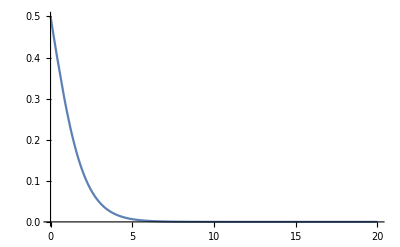

```mathematica
Plot[interpolatedDistEl[[20]][x],{x,0,20},PlotRange->All]
```

```mathematica
f3El=Interpolation[Transpose[{aEllist,#[3]&/@interpolatedDistEl}]];
f5El=Interpolation[Transpose[{aEllist,#[5]&/@interpolatedDistEl}]];
f7El=Interpolation[Transpose[{aEllist,#[7]&/@interpolatedDistEl}]];
```

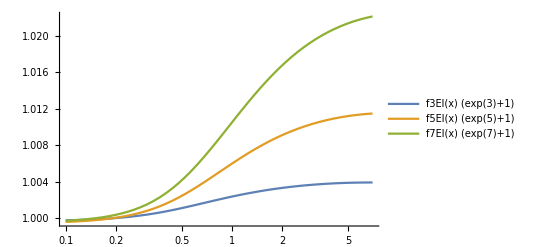

```mathematica
LogLinearPlot[{f3El[x]*(Exp[3]+1),f5El[x]*(Exp[5]+1),f7El[x]*(Exp[7]+1)},{x,0.1,7},PlotLegends->"Expressions"]
```

```mathematica
f3El[0.1]*(Exp[3]+1)-1
f5El[0.1]*(Exp[5]+1)-1
f7El[0.1]*(Exp[7]+1)-1
```

-0.000228134

-0.000403197

-0.000281346

```mathematica
(*sm-deltafnue_comp.eps*)
deltafnueTest=Import["../../figures/Figures-sources/sm-deltafnue_comp/semi_sm_upd_x.dat","HeaderLines"->2];
deltafnue3TestFunc=Interpolation[deltafnueTest[[All,{1,13}]]];
deltafnue5TestFunc=Interpolation[deltafnueTest[[All,{1,14}]]];
deltafnue7TestFunc=Interpolation[deltafnueTest[[All,{1,15}]]];
```

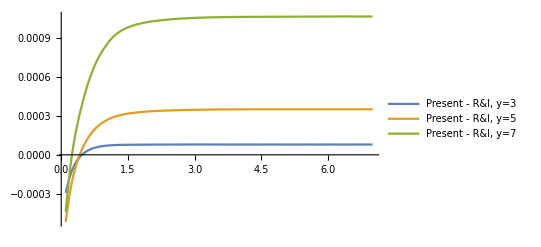

```mathematica
Show[Plot[{(f3El[x]-deltafnue3TestFunc[x])*(Exp[3]+1),(f5El[x]-deltafnue5TestFunc[x])*(Exp[5]+1),(f7El[x]-deltafnue7TestFunc[x])*(Exp[7]+1)},{x,0.1,7},PlotLegends->{"Present - R&I, y=3","Present - R&I, y=5","Present - R&I, y=7"}]]
```

```mathematica
deltafnue3Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue3-semi.dat","HeaderLines"->1];
deltafnue5Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue5-semi.dat","HeaderLines"->1];
deltafnue7Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue7-semi.dat","HeaderLines"->1];

deltafnue3DigitFunc=Interpolation[deltafnue3Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue5DigitFunc=Interpolation[deltafnue5Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue7DigitFunc=Interpolation[deltafnue7Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
f7El[0.1]*(Exp[7]+1)-1
```

-0.000281346

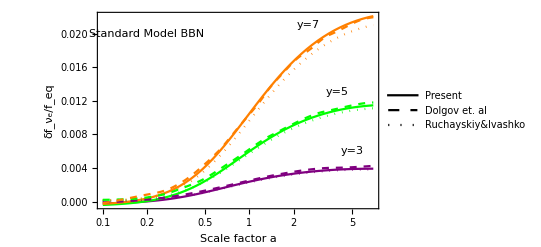

```mathematica
Show[LogLinearPlot[{f3El[x]*(Exp[3]+1)-1,f5El[x]*(Exp[5]+1)-1,f7El[x]*(Exp[7]+1)-1,deltafnue3TestFunc[x]*(Exp[3]+1)-1,deltafnue5TestFunc[x]*(Exp[5]+1)-1,deltafnue7TestFunc[x]*(Exp[7]+1)-1,deltafnue3DigitFunc[x],deltafnue5DigitFunc[x],deltafnue7DigitFunc[x]},{x,0.1,7},PlotRange->All(*{{0.1,7},{0,0.025}}*),Frame->True,FrameLabel->{"Scale factor a","δf_ν_e/f_eq"},PlotStyle->{{Purple},{Green},{Orange},{Purple,Dotted},{Green,Dotted},{Orange,Dotted},{Purple,Dashed},{Green,Dashed},{Orange,Dashed}},Epilog->{Text["Standard Model BBN",{Log[0.2],0.02}],Text["y=3",{Log[5],0.006}],Text["y=5",{Log[4],0.013}],Text["y=7",{Log[2.5],0.021}]},PlotLegends->LineLegend[{Thick,Dashed,Dotted},{"Present","Dolgov et. al","Ruchayskiy&Ivashko"}](*PlotLegends->{"Present, y=3","Present, y=5","Present, y=7","R&I, y=3","R&I, y=5","R&I, y=7","Dolgov, y=3","Dolgov, y=5","Dolgov, y=7"}*)]]
Export["final-spectra-SM-357-El.eps",%];
```

### Muon neutrinos

```mathematica
aμlist=First[Transpose[linesμ]];
```

```mathematica
setofdistributionsμ=Transpose[Transpose[linesμ][[3 ;;]]];
```

```mathematica
setofdistributionsμ1=Transpose[{yμ,#}]&/@setofdistributionsμ;
```

```mathematica
interpolatedDistμ=Interpolation/@setofdistributionsμ1;
```

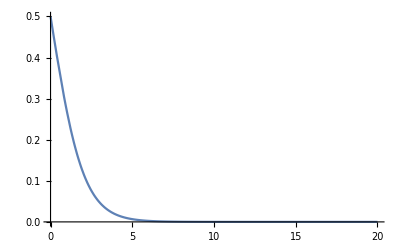

```mathematica
Plot[interpolatedDistμ[[20]][x],{x,0,20},PlotRange->All]
```

```mathematica
f3μ=Interpolation[Transpose[{aμlist,#[3]&/@interpolatedDistμ}]];
f5μ=Interpolation[Transpose[{aμlist,#[5]&/@interpolatedDistμ}]];
f7μ=Interpolation[Transpose[{aμlist,#[7]&/@interpolatedDistμ}]];
```

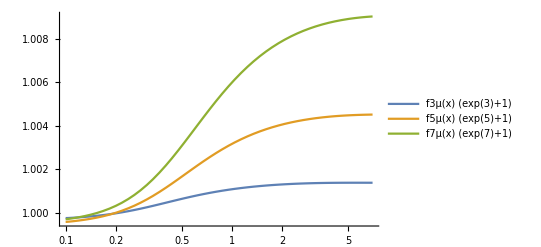

```mathematica
LogLinearPlot[{f3μ[x]*(Exp[3]+1),f5μ[x]*(Exp[5]+1),f7μ[x]*(Exp[7]+1)},{x,0.1,7},PlotLegends->"Expressions"]
```

```mathematica
f3μ[0.1]*(Exp[3]+1)-1
f5μ[0.1]*(Exp[5]+1)-1
f7μ[0.1]*(Exp[7]+1)-1
```

-0.000227752

-0.000402889

-0.000281133

```mathematica
(*sm-deltafnuμ_comp.eps*)
deltafnuμTest=Import["../../figures/Figures-sources/sm-deltafnumu_comp/semi_sm_upd_x.dat","HeaderLines"->2];
deltafnuμ3TestFunc=Interpolation[deltafnuμTest[[All,{1,27}]]];
deltafnuμ5TestFunc=Interpolation[deltafnuμTest[[All,{1,28}]]];
deltafnuμ7TestFunc=Interpolation[deltafnuμTest[[All,{1,29}]]];
```

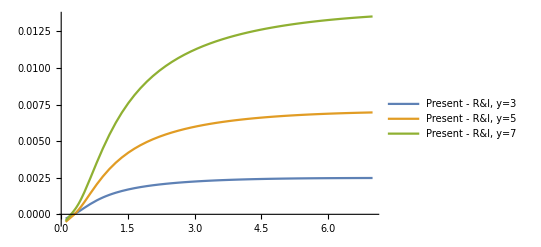

```mathematica
Show[Plot[{(f3El[x]-deltafnuμ3TestFunc[x])*(Exp[3]+1),(f5El[x]-deltafnuμ5TestFunc[x])*(Exp[5]+1),(f7El[x]-deltafnuμ7TestFunc[x])*(Exp[7]+1)},{x,0.1,7},PlotLegends->{"Present - R&I, y=3","Present - R&I, y=5","Present - R&I, y=7"}]]
```

```mathematica
deltafnuμ3Digit=Import["../../figures/Figures-sources/sm-deltafnumu_comp/sm-dfnumu3-semi.dat","HeaderLines"->1];
deltafnuμ5Digit=Import["../../figures/Figures-sources/sm-deltafnumu_comp/sm-dfnumu5-semi.dat","HeaderLines"->1];
deltafnuμ7Digit=Import["../../figures/Figures-sources/sm-deltafnumu_comp/sm-dfnumu7-semi.dat","HeaderLines"->1];

deltafnuμ3DigitFunc=Interpolation[deltafnuμ3Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnuμ5DigitFunc=Interpolation[deltafnuμ5Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnuμ7DigitFunc=Interpolation[deltafnuμ7Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
(f5μ[5]*(Exp[5]+1)-deltafnuμ5DigitFunc[5]-1)/deltafnuμ5DigitFunc[5]
```

-0.112188

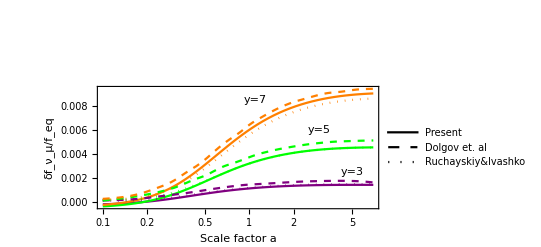

```mathematica
Show[LogLinearPlot[{f3μ[x]*(Exp[3]+1)-1,f5μ[x]*(Exp[5]+1)-1,f7μ[x]*(Exp[7]+1)-1,deltafnuμ3TestFunc[x]*(Exp[3]+1)-1,deltafnuμ5TestFunc[x]*(Exp[5]+1)-1,deltafnuμ7TestFunc[x]*(Exp[7]+1)-1,deltafnuμ3DigitFunc[x],deltafnuμ5DigitFunc[x],deltafnuμ7DigitFunc[x]},{x,0.1,7},PlotRange->All(*{{0.1,7},{0,0.025}}*),Frame->True,FrameLabel->{"Scale factor a","δf_ν_μ/f_eq"},PlotStyle->{{Purple},{Green},{Orange},{Purple,Dotted},{Green,Dotted},{Orange,Dotted},{Purple,Dashed},{Green,Dashed},{Orange,Dashed}},Epilog->{Text["Standard Model BBN",{Log[0.2],0.02}],Text["y=3",{Log[5],0.0025}],Text["y=5",{Log[3],0.006}],Text["y=7",{Log[1.1],0.0085}]},PlotLegends->LineLegend[{Thick,Dashed,Dotted},{"Present","Dolgov et. al","Ruchayskiy&Ivashko"}](*PlotLegends->{"Present, y=3","Present, y=5","Present, y=7","R&I, y=3","R&I, y=5","R&I, y=7","Dolgov, y=3","Dolgov, y=5","Dolgov, y=7"}*)]]
Export["final-spectra-SM-357-mu.eps",%];
```

### Comparison with Fig 1 of Mangano’s paper

```mathematica
f10El=Interpolation[Transpose[{0.5*aEllist,#[10]&/@interpolatedDistEl}]];
f10μ=Interpolation[Transpose[{0.5*aμlist,#[10]&/@interpolatedDistμ}]];
```

```mathematica
f10El[0.1]*(Exp[10]+1)-1
```

0.000287742

```mathematica
f10μ[0.1]*(Exp[10]+1)-1
```

0.000241493

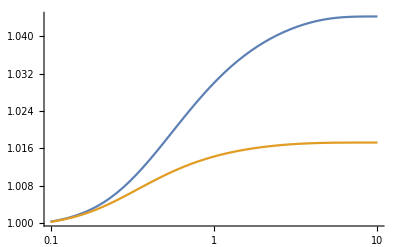

```mathematica
LogLinearPlot[{f10El[x]*(Exp[10]+1),f10μ[x]*(Exp[10]+1)},{x,0.1,10},Ticks -> Automatic]
```

```mathematica
deltafnue10Mangano=Import["../../figures/Figures-sources/sm-deltafnue_comp/mangano_dfn-nue-y10.dat","HeaderLines"->1];
deltafnue10ManganoFunc=Interpolation[deltafnue10Mangano[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
deltafnuμ10Mangano=Import["../../figures/Figures-sources/sm-deltafnumu_comp/mangano_dfn-numu-y10.dat","HeaderLines"->1];
deltafnuμ10ManganoFunc=Interpolation[deltafnuμ10Mangano[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
(deltafnuμ10ManganoFunc[10]-f10μ[10]*(Exp[10]+1))/(f10μ[10]*(Exp[10]+1))
```

0.00224165

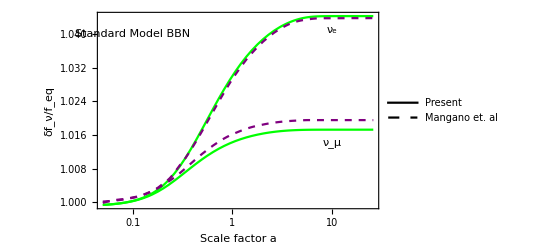

```mathematica
Show[LogLinearPlot[{f10El[x]*(Exp[10]+1),f10μ[x]*(Exp[10]+1),deltafnue10ManganoFunc[x],deltafnuμ10ManganoFunc[x]},{x,0.05,26},PlotRange->All(*{{0.1,7},{0,0.025}}*),Frame->True,FrameLabel->{"Scale factor a","δf_ν/f_eq"},PlotStyle->{{Green},{Green},{Purple, Dashed},{Purple, Dashed}},Epilog->{Text["Standard Model BBN",{Log[0.1],1.04}],Text["ν_e",{Log[10],1.041}],Text["ν_μ",{Log[10],1.014}]},PlotLegends->LineLegend[{Thick,Dashed},{"Present","Mangano et. al"}]]]
Export["final-spectra-SM-10.eps",%];
```

## Convergence of the collision integral (draft)

```mathematica
rawlinesCollEl = Import["./output0015625/Electron_neutrino.collision_integrals.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesCollEl = Rest[StringSplit/@rawlinesCollEl[[3;; ;; 10]]];
```

```mathematica
linesCollEl[[1]]
```

{0.000000000000000000e+00,-6.376551198172819568e-06,-6.227224957910948433e-07,4.791288592542741753e-06,7.991897597037223022e-06,9.116428882904870079e-06,8.827043069814521914e-06,7.783045612441696903e-06,6.461395498646993474e-06,5.147396826554739846e-06,3.982672331925840581e-06,3.015098233305479880e-06,2.245783121135325189e-06,1.651567106963902631e-06,1.202397350574813117e-06,8.683250352081728352e-07,6.228274898600894005e-07,4.442192712977854896e-07,3.153199775590698195e-07,2.228971688819636476e-07,1.569858242705945983e-07,1.102116721322932147e-07,7.715501718422168587e-08,5.387603768496063150e-08,3.753390729298311523e-08,2.609355751869574247e-08,1.810549164153046897e-08,1.254094134312336295e-08,8.672672857645835620e-09,5.988645964218920759e-09,4.129590231512388077e-09,2.843984138088066077e-09,1.956247033666532603e-09,1.344113933517262702e-09,9.225457435469135853e-10,6.325871773561926592e-10,4.333566970847252051e-10,2.966162853732640624e-10,2.028549826352905525e-10,1.386218653326974377e-10,9.465884963853179925e-11,6.459106943657760055e-11,4.404477064931375989e-11,3.001471287630104109e-11,2.044027658169885581e-11,1.391215617706083828e-11,9.462971089199462196e-12,6.432755554380496495e-12,4.370313241224503932e-12,2.967218958879941549e-12}

```mathematica
ICollEl = Map[Read[StringToStream[#],Number]&, linesCollEl, {2}];
```

```mathematica
yCollEl=Map[Read[StringToStream[#],Number]&,StringSplit[rawlinesCollEl[[1]]][[2;;]]];
```

```mathematica
Tlist=Select[Transpose[linesEl][[2]],#≤7&];
```

```mathematica
Length[Tlist]-Length[Max/@(Abs/@ICollEl)]
```

-22

```mathematica
Max/@(Abs/@ICollEl)
```

{9.11642888290487008×10^-6,0.0000116541959016558394,0.0000128570792590210203,0.0000138423265561016251,0.0000145905217330266623,0.0000151992287911184576,0.0000157355762553379464,0.0000162384450952401949,0.0000167287030627960576,0.0000172173299262112778,0.0000177101307841098787,0.0000182102229651093239,0.0000187193147560549278,0.0000192383633645931695,0.0000197679163171926575,0.0000203082910132934558,0.0000208596706841035484,0.0000214221553562765621,0.0000219957902025669227,0.0000225805813158785895,0.0000231765031344366435,0.0000237835035221678481,0.0000244015055095303524,0.0000250304083770913621,0.0000256700876910542775,0.0000263203950190415981,0.0000269811581077306073,0.0000276521804387641623,0.0000283332391859403288,0.0000290240853395573595,0.0000297244440972121993,0.0000304340130519165086,0.0000311524617124803172,0.0000318794330311789054,0.0000326145392115506638,0.0000333573625432848075,0.0000341074573917410362,0.0000348643473202514542,0.000035627530774462457,0.0000364270955888201797,0.0000372957039829202586,0.0000381757070044841385,0.0000390667341587658257,0.000039968388598765614,0.0000408802401086205691,0.0000418018197922975787,0.0000427326332363975325,0.000043672150846774116,0.0000446198107706408109,0.0000455750181060921022,0.0000465371442626150156,0.00004750552726306978,0.0000484794720456704908,0.0000494582718157943191,0.0000504411515045433134,0.0000514273220542094123,0.0000524159672465884796,0.0000534062394930145956,0.0000543972716737783912,0.0000553881534237632422,0.000056377955379716127,0.0000573657325553256214,0.0000583505048190602338,0.0000593312985941452098,0.0000603070895799362461,0.0000612768521435214097,0.0000622395350902138489,0.0000631940872075631432,0.0000641394472289391615,0.0000650745536923125201,0.0000659983304807099103,0.0000669096961303239368,0.0000678075915860887335,0.0000686910194502843297,0.0000695588568966343246,0.00007041006452546128,0.0000712436178673669929,0.0000720585129876383235,0.0000728537566985210106,0.000073628381880297411,0.0000743814398429520907,0.0000753215373539006805,0.0000762654428321241085,0.0000771911594465990447,0.0000780975953507123677,0.000078983684179689817,0.0000798483678998707092,0.0000806907069872409011,0.0000815096397221992675,0.0000823041929898238323,0.0000830736053192282498,0.0000838169034356184284,0.0000845333128562941738,0.0000852220024505356832,0.0000858822214677701368,0.0000865132898919540594,0.0000871145484460100761,0.0000876854856723952025,0.0000882256030010353243,0.0000887344471056650264,0.0000892114840223001693,0.0000896563427588148443,0.000090068696794176617,0.0000904482530206252022,0.0000907949739925584254,0.0000911087576849212155,0.0000913892760490142564,0.0000916367781567117845,0.0000918512026881757038,0.0000920325198450200332,0.0000921808030618365137,0.0000922963748450911226,0.0000923793477092260673,0.0000924304083049776182,0.0000924494649989782147,0.0000924366318244551621,0.0000923933188357040081,0.0000923193268675959189,0.000092215105746973336,0.0000920811382787434241,0.0000919177810487781244,0.0000917260152633048165,0.0000915062902340224582,0.0000912598145585974407,0.0000909866767617728556,0.000090687841449721418,0.000090363720692820948,0.0000900373942780419156,0.0000898120891790199494,0.0000895603232153874274,0.0000892822688713934554,0.0000889797439640460652,0.0000886526086762984278,0.0000883014805497239763,0.0000879268719478076832,0.0000875295998525871255,0.0000871112859002209916,0.0000866712705072103518,0.0000862117529942807437,0.0000857324463110487045,0.0000852350720759176284,0.0000847193801245538225,0.000084185551880722187,0.000083634879439742349,0.0000830689465125544757,0.0000824864273818448623,0.000081891144803059035,0.0000812836987673648537,0.0000806631550043235279,0.0000800271465406510174,0.0000793753505012873006,0.0000787119235923228189,0.0000780376849274233564,0.0000773516826368947363,0.0000766624494108469889,0.0000759654676008025831,0.0000752604268683398914,0.0000745477986008324933,0.0000738272524269945052,0.000073099941935161894,0.0000723695015381053963,0.0000716250804666529461,0.0000708775326963007046,0.000070124647000291418,0.0000693662803863404065,0.0000686022212814663135,0.0000678286647115555752,0.0000670579439354668239,0.0000662846513632686651,0.0000655054749154615479,0.0000647286229815691172,0.0000639568375015997503,0.0000631823754559945883,0.0000624066157195457549,0.0000616275774900643114,0.0000608559994264012971,0.0000600834090302981849,0.0000592995822890074464,0.000058519797772049742,0.0000577450063454776341,0.0000569691988427933893,0.0000562022326455746679,0.0000554312020684122331,0.0000546700315018355809,0.0000539089583062590805,0.0000531426258687517361,0.0000523887319259230821,0.0000516276821604932934,0.0000508699470502804729,0.0000501281154985377953,0.0000493812626967127244,0.0000486393150112007788,0.0000478950341120665257,0.0000471444183514080351,0.0000463983243692567271,0.0000456380487001695201,0.0000449180391948189595,0.0000442130975653043379,0.000043503453790449953,0.0000428019983855776331,0.000042098186692207662,0.0000413872305715656808,0.0000406718404066808148,0.0000399471890544234043,0.000039280868300295424,0.0000386229499271806276,0.0000379605111477943069,0.0000373061621150583278,0.0000366375031379817528,0.0000359466331234514769,0.0000352658673019590196,0.0000345625891196021939,0.0000339075529520727059,0.0000332425168325656273,0.0000325659517663723364,0.0000319169055718049322,0.0000312498452759157885,0.000030556425008043675,0.0000298541526921880518,0.0000291496452398121164,0.0000284951604179184415,0.0000278605271075704764,0.0000271936179707665815,0.000026586401498107648,0.0000259326273299720356,0.0000252364650643599475,0.000024536370473171587,0.0000239332687490545482,0.0000233670043359168744,0.0000227762732940561818,0.0000221430070279637903,0.0000215154280835960776,0.0000209533086747981656,0.0000204446108220679435,0.000019906401185210143,0.0000192842004986815141,0.0000187290647568616464,0.000018140432698210418,0.0000175630388321579289,0.000016969807949962501,0.0000164906327526637142,0.0000159725784110165137,0.0000153818507753200606,0.00001478815882638429,0.0000142603703867649756,0.0000137218598528221492,0.0000131846789264145059,0.0000127002115446472885,0.0000122166514415766869,0.0000117125147536256691,0.0000112084595316197522,0.0000107685202599405727,0.0000103844970467115161,9.9112677554025197×10^-6,9.48631927011334142×10^-6,9.03573246668898378×10^-6,8.66411806299538512×10^-6,8.43259881477820272×10^-6,8.20794653577650024×10^-6,7.98305929805565029×10^-6,7.74552693982855089×10^-6,7.4814322914562581×10^-6,7.22072750036772959×10^-6,6.969288151026376×10^-6,6.70967661875465637×10^-6,6.44111166181460249×10^-6,6.17614626108320408×10^-6,5.9196853996468235×10^-6,5.66193460116437564×10^-6,5.4047109365740198×10^-6,5.15596049410760315×10^-6,4.91237678090783447×10^-6,4.67234039902564291×10^-6,4.43963207530373438×10^-6,4.21477093226485522×10^-6,3.99572654075086575×10^-6,3.78491485264476069×10^-6,3.58156761137706781×10^-6,3.39671681004460879×10^-6,3.23617733499759197×10^-6,3.08048424102480567×10^-6,2.92518151923104597×10^-6,2.77369158752094336×10^-6,2.62782505089376173×10^-6,2.48449604001166335×10^-6,2.34651492903026337×10^-6,2.21381418086252779×10^-6,2.08529893797049226×10^-6,1.96242675443158987×10^-6,1.8444758964619723×10^-6,1.73174971251910392×10^-6,1.62407712167578211×10^-6,1.52147439536065576×10^-6,1.42383555612468626×10^-6,1.33110580335937812×10^-6,1.2430595042189907×10^-6,1.15963260327589524×10^-6,1.08063769488353501×10^-6,1.00593405605309272×10^-6,9.35408959179540034×10^-7,8.68907914508554313×10^-7,8.06252202778523497×10^-7,7.47316430960154321×10^-7,6.91895269966380511×10^-7,6.39837978155810561×10^-7,5.90996087623807398×10^-7,5.45270353313753731×10^-7,5.02496728671530946×10^-7,4.62523619404464625×10^-7,4.25201633902361209×10^-7,3.90365979541229535×10^-7,3.57910110437842377×10^-7,3.27701421554138506×10^-7,2.99666549352650691×10^-7,2.73676565853975262×10^-7,2.49599931834154631×10^-7,2.27325180901516433×10^-7,2.0672704437174616×10^-7,1.87705975207563824×10^-7,1.70180793901408833×10^-7,1.54067585356187919×10^-7,1.39291085332615694×10^-7,1.25746595358577906×10^-7,1.13342579766140261×10^-7,1.02010169200639211×10^-7,9.16609188550410181×10^-8,8.22250711962624337×10^-8,7.36445393556550698×10^-8,6.58754828464225284×10^-8,5.88433657355835749×10^-8,5.24829957271322201×10^-8,4.67407090809501824×10^-8,4.15647427587373386×10^-8,3.69144004253030289×10^-8,3.2737581534547644×10^-8,2.89953838716883183×10^-8,2.56587107116956759×10^-8,2.26861018859381147×10^-8,2.00393479588001355×10^-8,1.76864034528989578×10^-8,1.55992374573088455×10^-8,1.37500677510615788×10^-8,1.21156773502661963×10^-8,1.06751762984913512×10^-8,9.41032141099640285×10^-9,8.2993345529303042×10^-9,7.32427452021511272×10^-9,6.56338983162640943×10^-9,5.90565818470167869×10^-9,5.32608623871055897×10^-9,4.81522377526744094×10^-9,4.36507718859502347×10^-9,3.96996213680722576×10^-9,3.62218699478944473×10^-9,3.36264349698467413×10^-9,3.14450687710632337×10^-9,2.9467983608810755×10^-9,2.76735079296486219×10^-9,2.60346411096179509×10^-9,2.4531843223485339×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ICollMaximums=Transpose[{Tlist,Max/@(Abs/@ICollEl)}]
```

Transpose::nmtx: The first two levels of {{6.99229,6.8839,6.77719,6.67213,6.5687,6.46688,6.36664,6.26795,6.17079,6.07514,5.98097,5.88826,5.79699,5.70714,5.61867,5.53158,5.44584,«17»,4.11112,4.04741,3.98469,3.92294,3.86215,3.80231,3.74339,3.68538,3.62828,3.57206,3.51672,3.46223,3.40859,3.35578,3.30379,3.25261,«553»},{«1»}} cannot be transposed.

Transpose[{{6.99229,6.8839,6.77719,6.67213,6.5687,6.46688,6.36664,6.26795,6.17079,6.07514,5.98097,5.88826,5.79699,5.70714,5.61867,5.53158,5.44584,5.36143,5.27833,5.19652,5.11598,5.03668,4.95862,4.88176,4.8061,4.73161,4.65828,4.58608,4.51501,4.44504,4.37615,4.30833,4.24156,4.17583,4.11112,4.04741,3.98469,3.92294,3.86215,3.80231,3.74339,3.68538,3.62828,3.57206,3.51672,3.46223,3.40859,3.35578,3.30379,3.25261,3.20222,3.15262,3.10378,3.0557,3.00837,2.96178,2.9159,2.87074,2.82628,2.78251,2.73942,2.697,2.65524,2.61412,2.57365,2.5338,2.49457,2.45596,2.41794,2.38051,2.34367,2.30739,2.27168,2.23653,2.20192,2.16785,2.13431,2.10129,2.06878,2.03678,2.00528,1.97427,1.94374,1.91368,1.88409,1.85497,1.82629,1.79806,1.77027,1.74292,1.71599,1.68948,1.66338,1.63769,1.6124,1.5875,1.56299,1.53886,1.51511,1.49173,1.46871,1.44606,1.42375,1.4018,1.38018,1.35891,1.33796,1.31734,1.29705,1.27707,1.2574,1.23804,1.21899,1.20023,1.18176,1.16359,1.1457,1.12808,1.11075,1.09368,1.07688,1.06035,1.04407,1.02805,1.01228,0.996757,0.981478,0.966438,0.951635,0.937063,0.922721,0.908604,0.894709,0.881032,0.86757,0.85432,0.841279,0.828443,0.815809,0.803374,0.791135,0.779089,0.767233,0.755564,0.74408,0.732776,0.721652,0.710703,0.699927,0.689322,0.678885,0.668613,0.658503,0.648554,0.638763,0.629127,0.619645,0.610312,0.601129,0.592091,0.583197,0.574444,0.565831,0.557355,0.549015,0.540807,0.53273,0.524783,0.516962,0.509266,0.501694,0.494243,0.486911,0.479696,0.472597,0.465612,0.458739,0.451976,0.445322,0.438775,0.432333,0.425995,0.419759,0.413623,0.407586,0.401646,0.395802,0.390052,0.384395,0.378829,0.373353,0.367965,0.362664,0.357449,0.352318,0.34727,0.342304,0.337418,0.33261,0.327881,0.323227,0.318649,0.314145,0.309713,0.305353,0.301063,0.296843,0.29269,0.288604,0.284584,0.280629,0.276737,0.272908,0.26914,0.265432,0.261784,0.258194,0.254662,0.251186,0.247765,0.244398,0.241085,0.237825,0.234616,0.231458,0.228349,0.225289,0.222278,0.219313,0.216395,0.213522,0.210694,0.207909,0.205168,0.202468,0.19981,0.197193,0.194615,0.192077,0.189577,0.187115,0.184689,0.1823,0.179946,0.177627,0.175342,0.173091,0.170873,0.168686,0.166532,0.164408,0.162314,0.16025,0.158215,0.156209,0.154231,0.15228,0.150355,0.148457,0.146585,0.144738,0.142916,0.141117,0.139343,0.137591,0.135862,0.134155,0.13247,0.130806,0.129163,0.12754,0.125938,0.124354,0.12279,0.121244,0.119717,0.118207,0.116715,0.11524,0.113782,0.11234,0.110914,0.109503,0.108108,0.106729,0.105363,0.104013,0.102676,0.101353,0.100044,0.0987478,0.0974649,0.0961948,0.0949373,0.0936921,0.0924591,0.091238,0.0900287,0.088831,0.0876446,0.0864696,0.0853057,0.0841528,0.0830108,0.0818795,0.0807589,0.079649,0.0785495,0.0774606,0.076382,0.0753139,0.0742561,0.0732086,0.0721715,0.0711447,0.0701282,0.0691221,0.0681264,0.067141,0.0661661,0.0652017,0.0642478,0.0633044,0.0623716,0.0614495,0.060538,0.0596372,0.0587471,0.0578679,0.0569994,0.0561417,0.0552949,0.0544589,0.0536338,0.0528195,0.052016,0.0512234,0.0504415,0.0496704,0.04891,0.0481603,0.0474212,0.0466926,0.0459745,0.0452668,0.0445694,0.0438823,0.0432053,0.0425383,0.0418813,0.0412341,0.0405967,0.0399688,0.0393505,0.0387415,0.0381418,0.0375513,0.0369698,0.0363972,0.0358333,0.0352782,0.0347316,0.0341934,0.0336635,0.0331417,0.0326281,0.0321223,0.0316244,0.0311342,0.0306516,0.0301764,0.0297086,0.029248,0.0287946,0.0283482,0.0279087,0.0274761,0.0270501,0.0266307,0.0262179,0.0258114,0.0254112,0.0250173,0.0246294,0.0242476,0.0238716,0.0235016,0.0231372,0.0227785,0.0224253,0.0220777,0.0217354,0.0213984,0.0210667,0.02074,0.0204185,0.0201019,0.0197903,0.0194835,0.0191814,0.018884,0.0185913,0.018303,0.0180193,0.0177399,0.0174649,0.0171941,0.0169275,0.0166651,0.0164067,0.0161524,0.0159019,0.0156554,0.0154127,0.0151737,0.0149385,0.0147069,0.0144789,0.0142544,0.0140334,0.0138159,0.0136017,0.0133908,0.0131832,0.0129788,0.0127776,0.0125795,0.0123845,0.0121924,0.0120034,0.0118173,0.0116341,0.0114537,0.0112762,0.0111014,0.0109292,0.0107598,0.010593,0.0104288,0.0102671,0.0101079,0.00995118,0.0097969,0.00964502,0.00949548,0.00934827,0.00920334,0.00906065,0.00892018,0.00878189,0.00864574,0.0085117,0.00837974,0.00824982,0.00812192,0.007996,0.00787203,0.00774999,0.00762984,0.00751155,0.00739509,0.00728044,0.00716757,0.00705644,0.00694704,0.00683934,0.00673331,0.00662892,0.00652614,0.00642497,0.00632536,0.00622729,0.00613075,0.0060357,0.00594212,0.00585,0.0057593,0.00567001,0.00558211,0.00549556,0.00541036,0.00532648,0.0052439,0.00516261,0.00508257,0.00500377,0.00492619,0.00484982,0.00477463,0.00470061,0.00462773,0.00455598,0.00448535,0.00441581,0.00434735,0.00427995,0.0042136,0.00414827,0.00408396,0.00402064,0.00395831,0.00389694,0.00383652,0.00377704,0.00371849,0.00366084,0.00360408,0.0035482,0.00349319,0.00343904,0.00338572,0.00333323,0.00328155,0.00323068,0.00318059,0.00313128,0.00308273,0.00303494,0.00298789,0.00294156,0.00289596,0.00285106,0.00280686,0.00276334,0.0027205,0.00267832,0.0026368,0.00259592,0.00255568,0.00251605,0.00247705,0.00243864,0.00240083,0.00236361,0.00232697,0.00229089,0.00225538,0.00222041,0.00218598,0.00215209,0.00211873,0.00208588,0.00205354,0.00202171,0.00199036,0.0019595,0.00192913,0.00189922,0.00186977,0.00184078,0.00181225,0.00178415,0.00175649,0.00172926,0.00170245,0.00167605,0.00165007,0.00162449,0.0015993,0.00157451,0.0015501,0.00152606,0.0015024,0.00147911,0.00145618,0.0014336,0.00141138,0.0013895,0.00136795,0.00134675,0.00132587,0.00130531,0.00128507,0.00126515,0.00124554,0.00122623,0.00120722,0.0011885,0.00117007,0.00115193,0.00113407,0.00111649,0.00109918,0.00108214,0.00106536,0.00104885,0.00103259,0.00101658,0.00100082,0.0009853,0.000970025,0.000954986,0.00094018,0.000925604,0.000911254,0.000897126,0.000883218,0.000869525,0.000856044,0.000842772,0.000829706,0.000816843,0.000804179},{9.11642888290487008×10^-6,0.0000116541959016558394,0.0000128570792590210203,0.0000138423265561016251,0.0000145905217330266623,0.0000151992287911184576,0.0000157355762553379464,0.0000162384450952401949,0.0000167287030627960576,0.0000172173299262112778,0.0000177101307841098787,0.0000182102229651093239,0.0000187193147560549278,0.0000192383633645931695,0.0000197679163171926575,0.0000203082910132934558,0.0000208596706841035484,0.0000214221553562765621,0.0000219957902025669227,0.0000225805813158785895,0.0000231765031344366435,0.0000237835035221678481,0.0000244015055095303524,0.0000250304083770913621,0.0000256700876910542775,0.0000263203950190415981,0.0000269811581077306073,0.0000276521804387641623,0.0000283332391859403288,0.0000290240853395573595,0.0000297244440972121993,0.0000304340130519165086,0.0000311524617124803172,0.0000318794330311789054,0.0000326145392115506638,0.0000333573625432848075,0.0000341074573917410362,0.0000348643473202514542,0.000035627530774462457,0.0000364270955888201797,0.0000372957039829202586,0.0000381757070044841385,0.0000390667341587658257,0.000039968388598765614,0.0000408802401086205691,0.0000418018197922975787,0.0000427326332363975325,0.000043672150846774116,0.0000446198107706408109,0.0000455750181060921022,0.0000465371442626150156,0.00004750552726306978,0.0000484794720456704908,0.0000494582718157943191,0.0000504411515045433134,0.0000514273220542094123,0.0000524159672465884796,0.0000534062394930145956,0.0000543972716737783912,0.0000553881534237632422,0.000056377955379716127,0.0000573657325553256214,0.0000583505048190602338,0.0000593312985941452098,0.0000603070895799362461,0.0000612768521435214097,0.0000622395350902138489,0.0000631940872075631432,0.0000641394472289391615,0.0000650745536923125201,0.0000659983304807099103,0.0000669096961303239368,0.0000678075915860887335,0.0000686910194502843297,0.0000695588568966343246,0.00007041006452546128,0.0000712436178673669929,0.0000720585129876383235,0.0000728537566985210106,0.000073628381880297411,0.0000743814398429520907,0.0000753215373539006805,0.0000762654428321241085,0.0000771911594465990447,0.0000780975953507123677,0.000078983684179689817,0.0000798483678998707092,0.0000806907069872409011,0.0000815096397221992675,0.0000823041929898238323,0.0000830736053192282498,0.0000838169034356184284,0.0000845333128562941738,0.0000852220024505356832,0.0000858822214677701368,0.0000865132898919540594,0.0000871145484460100761,0.0000876854856723952025,0.0000882256030010353243,0.0000887344471056650264,0.0000892114840223001693,0.0000896563427588148443,0.000090068696794176617,0.0000904482530206252022,0.0000907949739925584254,0.0000911087576849212155,0.0000913892760490142564,0.0000916367781567117845,0.0000918512026881757038,0.0000920325198450200332,0.0000921808030618365137,0.0000922963748450911226,0.0000923793477092260673,0.0000924304083049776182,0.0000924494649989782147,0.0000924366318244551621,0.0000923933188357040081,0.0000923193268675959189,0.000092215105746973336,0.0000920811382787434241,0.0000919177810487781244,0.0000917260152633048165,0.0000915062902340224582,0.0000912598145585974407,0.0000909866767617728556,0.000090687841449721418,0.000090363720692820948,0.0000900373942780419156,0.0000898120891790199494,0.0000895603232153874274,0.0000892822688713934554,0.0000889797439640460652,0.0000886526086762984278,0.0000883014805497239763,0.0000879268719478076832,0.0000875295998525871255,0.0000871112859002209916,0.0000866712705072103518,0.0000862117529942807437,0.0000857324463110487045,0.0000852350720759176284,0.0000847193801245538225,0.000084185551880722187,0.000083634879439742349,0.0000830689465125544757,0.0000824864273818448623,0.000081891144803059035,0.0000812836987673648537,0.0000806631550043235279,0.0000800271465406510174,0.0000793753505012873006,0.0000787119235923228189,0.0000780376849274233564,0.0000773516826368947363,0.0000766624494108469889,0.0000759654676008025831,0.0000752604268683398914,0.0000745477986008324933,0.0000738272524269945052,0.000073099941935161894,0.0000723695015381053963,0.0000716250804666529461,0.0000708775326963007046,0.000070124647000291418,0.0000693662803863404065,0.0000686022212814663135,0.0000678286647115555752,0.0000670579439354668239,0.0000662846513632686651,0.0000655054749154615479,0.0000647286229815691172,0.0000639568375015997503,0.0000631823754559945883,0.0000624066157195457549,0.0000616275774900643114,0.0000608559994264012971,0.0000600834090302981849,0.0000592995822890074464,0.000058519797772049742,0.0000577450063454776341,0.0000569691988427933893,0.0000562022326455746679,0.0000554312020684122331,0.0000546700315018355809,0.0000539089583062590805,0.0000531426258687517361,0.0000523887319259230821,0.0000516276821604932934,0.0000508699470502804729,0.0000501281154985377953,0.0000493812626967127244,0.0000486393150112007788,0.0000478950341120665257,0.0000471444183514080351,0.0000463983243692567271,0.0000456380487001695201,0.0000449180391948189595,0.0000442130975653043379,0.000043503453790449953,0.0000428019983855776331,0.000042098186692207662,0.0000413872305715656808,0.0000406718404066808148,0.0000399471890544234043,0.000039280868300295424,0.0000386229499271806276,0.0000379605111477943069,0.0000373061621150583278,0.0000366375031379817528,0.0000359466331234514769,0.0000352658673019590196,0.0000345625891196021939,0.0000339075529520727059,0.0000332425168325656273,0.0000325659517663723364,0.0000319169055718049322,0.0000312498452759157885,0.000030556425008043675,0.0000298541526921880518,0.0000291496452398121164,0.0000284951604179184415,0.0000278605271075704764,0.0000271936179707665815,0.000026586401498107648,0.0000259326273299720356,0.0000252364650643599475,0.000024536370473171587,0.0000239332687490545482,0.0000233670043359168744,0.0000227762732940561818,0.0000221430070279637903,0.0000215154280835960776,0.0000209533086747981656,0.0000204446108220679435,0.000019906401185210143,0.0000192842004986815141,0.0000187290647568616464,0.000018140432698210418,0.0000175630388321579289,0.000016969807949962501,0.0000164906327526637142,0.0000159725784110165137,0.0000153818507753200606,0.00001478815882638429,0.0000142603703867649756,0.0000137218598528221492,0.0000131846789264145059,0.0000127002115446472885,0.0000122166514415766869,0.0000117125147536256691,0.0000112084595316197522,0.0000107685202599405727,0.0000103844970467115161,9.9112677554025197×10^-6,9.48631927011334142×10^-6,9.03573246668898378×10^-6,8.66411806299538512×10^-6,8.43259881477820272×10^-6,8.20794653577650024×10^-6,7.98305929805565029×10^-6,7.74552693982855089×10^-6,7.4814322914562581×10^-6,7.22072750036772959×10^-6,6.969288151026376×10^-6,6.70967661875465637×10^-6,6.44111166181460249×10^-6,6.17614626108320408×10^-6,5.9196853996468235×10^-6,5.66193460116437564×10^-6,5.4047109365740198×10^-6,5.15596049410760315×10^-6,4.91237678090783447×10^-6,4.67234039902564291×10^-6,4.43963207530373438×10^-6,4.21477093226485522×10^-6,3.99572654075086575×10^-6,3.78491485264476069×10^-6,3.58156761137706781×10^-6,3.39671681004460879×10^-6,3.23617733499759197×10^-6,3.08048424102480567×10^-6,2.92518151923104597×10^-6,2.77369158752094336×10^-6,2.62782505089376173×10^-6,2.48449604001166335×10^-6,2.34651492903026337×10^-6,2.21381418086252779×10^-6,2.08529893797049226×10^-6,1.96242675443158987×10^-6,1.8444758964619723×10^-6,1.73174971251910392×10^-6,1.62407712167578211×10^-6,1.52147439536065576×10^-6,1.42383555612468626×10^-6,1.33110580335937812×10^-6,1.2430595042189907×10^-6,1.15963260327589524×10^-6,1.08063769488353501×10^-6,1.00593405605309272×10^-6,9.35408959179540034×10^-7,8.68907914508554313×10^-7,8.06252202778523497×10^-7,7.47316430960154321×10^-7,6.91895269966380511×10^-7,6.39837978155810561×10^-7,5.90996087623807398×10^-7,5.45270353313753731×10^-7,5.02496728671530946×10^-7,4.62523619404464625×10^-7,4.25201633902361209×10^-7,3.90365979541229535×10^-7,3.57910110437842377×10^-7,3.27701421554138506×10^-7,2.99666549352650691×10^-7,2.73676565853975262×10^-7,2.49599931834154631×10^-7,2.27325180901516433×10^-7,2.0672704437174616×10^-7,1.87705975207563824×10^-7,1.70180793901408833×10^-7,1.54067585356187919×10^-7,1.39291085332615694×10^-7,1.25746595358577906×10^-7,1.13342579766140261×10^-7,1.02010169200639211×10^-7,9.16609188550410181×10^-8,8.22250711962624337×10^-8,7.36445393556550698×10^-8,6.58754828464225284×10^-8,5.88433657355835749×10^-8,5.24829957271322201×10^-8,4.67407090809501824×10^-8,4.15647427587373386×10^-8,3.69144004253030289×10^-8,3.2737581534547644×10^-8,2.89953838716883183×10^-8,2.56587107116956759×10^-8,2.26861018859381147×10^-8,2.00393479588001355×10^-8,1.76864034528989578×10^-8,1.55992374573088455×10^-8,1.37500677510615788×10^-8,1.21156773502661963×10^-8,1.06751762984913512×10^-8,9.41032141099640285×10^-9,8.2993345529303042×10^-9,7.32427452021511272×10^-9,6.56338983162640943×10^-9,5.90565818470167869×10^-9,5.32608623871055897×10^-9,4.81522377526744094×10^-9,4.36507718859502347×10^-9,3.96996213680722576×10^-9,3.62218699478944473×10^-9,3.36264349698467413×10^-9,3.14450687710632337×10^-9,2.9467983608810755×10^-9,2.76735079296486219×10^-9,2.60346411096179509×10^-9,2.4531843223485339×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}]

```mathematica
ListLinePlot[ICollMaximums,PlotLabel->Style[#,Bold,15]&/@{"Icoll for electron neutrinos"},Frame-> True, FrameLabel->{"T [MeV]","Icoll"},PlotRange->All]
```

Transpose::nmtx: The first two levels of {{6.99229,6.8839,6.77719,6.67213,6.5687,6.46688,6.36664,6.26795,6.17079,6.07514,5.98097,5.88826,5.79699,5.70714,5.61867,5.53158,5.44584,«17»,4.11112,4.04741,3.98469,3.92294,3.86215,3.80231,3.74339,3.68538,3.62828,3.57206,3.51672,3.46223,3.40859,3.35578,3.30379,3.25261,«553»},{«1»}} cannot be transposed.

$Aborted[]

$Aborted

## δρ/ρ(eq)

### Figure 2 of Dolgov’s article

```mathematica
rawlinesρ = Import["./output0015625/rho_nu.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesρ = StringSplit/@rawlinesρ;
```

```mathematica
linesρ = Transpose[FileToNumLevel2[linesρ]];
```

```mathematica
alistρ=linesρ[[1]];
ρlistρ=linesρ[[2]];
```

```mathematica
ρeq=(7 π^2)/240*(1/#)^4&/@alistρ;
```

```mathematica
deltaρa=Interpolation[Transpose[{alistρ,ρlistρ/(6ρeq)-1}]] ;
```

```mathematica
deltaρaEncorserv=Import["../../figures/Figures-sources/sm-delta-rho_comp/delta_rho_entropy_conserv.dat","HeaderLines"->1];
deltaρaEnconservFunc=Interpolation[deltaρaEncorserv[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
deltaρaDolgov=Import["../../figures/Figures-sources/sm-delta-rho_comp/dolgov_rho.dat","HeaderLines"->1];
deltaρaDolgovFunc=Interpolation[deltaρaDolgov[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
deltaρaDolgovNonconserv=Import["../../figures/Figures-sources/sm-delta-rho_comp/dolgov_rho_entropy_nonconserv.dat","HeaderLines"->1];
```

```mathematica
deltaρaDolgovFuncNonconserv=Interpolation[deltaρaDolgovNonconserv[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

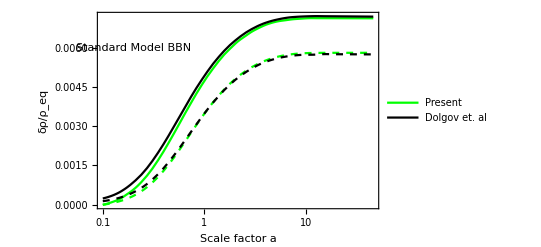

```mathematica
Show[LogLinearPlot[{deltaρa[x],deltaρaEnconservFunc[x],deltaρaDolgovFunc[x],deltaρaDolgovFuncNonconserv[x]},{x,0.1,46},PlotRange->All(*{{0.1,100},{0,0.008}}*),Frame->True,FrameLabel->{"Scale factor a","δρ/ρ_eq"},PlotStyle->{{Dashed,Green},{Thick,Green},{Black},{Dashed,Black}},Epilog->{Text["Standard Model BBN",{Log[0.2],0.006}]},PlotLegends->LineLegend[{Green,Black},{"Present","Dolgov et. al"}]]]
Export["delta_rho.eps",%];
```

```mathematica
"delta_rho.eps"
```

delta_rho.eps

#### Figure 1 from Hannestad&Madsen

```mathematica
rawlinesρEl = Import["./output0015625/Electron_neutrino.rho.txt", {"Text", "Lines"}][[2;; ]];
rawlinesρμ = Import["./output0015625/Muon_neutrino.rho.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesEl = FileToNumLevel2[StringSplit/@rawlinesρEl];
linesμ = FileToNumLevel2[StringSplit/@rawlinesρμ];
```

```mathematica
TEllist=Transpose[linesEl][[2]];
Tμlist=Transpose[linesμ][[2]];
```

```mathematica
aEllist=Transpose[linesEl][[1]];
aμlist=Transpose[linesμ][[1]];
```

```mathematica
ρlistρEl=Transpose[linesEl][[4]];
ρlistρμ=Transpose[linesμ][[4]];
```

```mathematica
ρeq0El=(7 π^2)/240(1/#)^4&/@aEllist;
ρeq0μ=(7 π^2)/240(1/#)^4&/@aμlist;
```

```mathematica
Length[ρeq0El]
```

625

```mathematica
deltaρTEl=Interpolation[Transpose[{TEllist,(ρlistρEl-2ρeq0El)/ρlistρEl}]];
deltaρTμ=Interpolation[Transpose[{Tμlist,(ρlistρμ-4ρeq0μ)/ρlistρμ}]];
```

```mathematica
(deltaρTEl[0.002]+deltaρTμ[0.002])/3-deltaρa[1/0.002]
```

-0.00133213

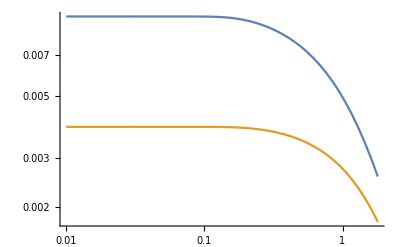

```mathematica
LogLogPlot[{deltaρTEl[x],deltaρTμ[x]},{x,0.01,1.8}]
```

```mathematica
deltaρTElHannestad=Import["../../figures/Figures-sources/sm-delta-rho_comp/Hannestad_rho_e_case1.dat","HeaderLines"->1];
deltaρTElHannestadFunc=Interpolation[deltaρTElHannestad[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
deltaρTμHannestad=Import["../../figures/Figures-sources/sm-delta-rho_comp/Hannestad_rho_mu_case1.dat","HeaderLines"->1];
deltaρTμHannestadFunc=Interpolation[deltaρTμHannestad[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
(deltaρTEl[0.5]-deltaρTElHannestadFunc[0.5])/deltaρTElHannestadFunc[0.5]
```

0.34304

```mathematica
(deltaρTEl[0.05]-deltaρTElHannestadFunc[0.05])/deltaρTElHannestadFunc[0.05]
```

0.135518

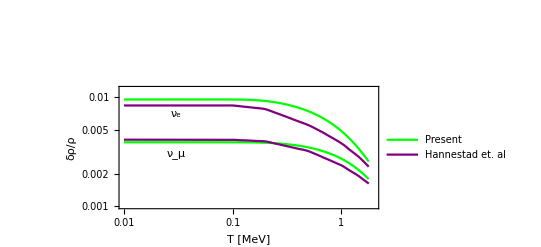

```mathematica
Show[LogLogPlot[{deltaρTEl[x],deltaρTμ[x],deltaρTElHannestadFunc[x],deltaρTμHannestadFunc[x]},{x,0.01,1.8},PlotRange->{{0.01,2},{0.001,0.012}},Frame->True,FrameLabel->{"T [MeV]","δρ/ρ"},PlotStyle->{{Thick,Green},{Thick,Green},{Purple},{Purple}},Epilog->{Text["Standard Model BBN",{Log[0.1],1.04}],Text["ν_e",{Log[0.03],Log[0.007]}],Text["ν_μ",{Log[0.03],Log[0.003]}]},PlotLegends->LineLegend[{Green,Purple},{"Present","Hannestad et. al"}]]]
```

```mathematica
Export["delta_rho_Hannestad.eps",%];
```

## Teff

### Comraring with figure 3 of Hannestad et. al

```mathematica
aT=aEllist* TEllist;
```

```mathematica
pEl=
```

```mathematica
plotDataEl=Transpose[{yEl, distEl1}];
```

Transpose::nmtx: The first two levels of {Read[$Failed,Number]⟦Read[$Failed,Number]⟧,StringSplit[Read[$Failed,Number]]⟦3;;All⟧} cannot be transposed.